# LinearModelFit Explanation

```mathematica
HMat = {{1,-40},{1,-24},{1,-8},{1,8},{1,24},{1,40}};
CoVar=Inverse[Transpose[HMat].HMat];
GMat=CoVar.Transpose[HMat];
PMat=HMat.GMat;
HMat//MatrixForm
CoVar//N//MatrixForm
GMat//N//MatrixForm
PMat//N//MatrixForm
NInput = Length[HMat]
NPara = Length[CoVar]
DF = NInput - NPara
```

(1 | -40
1 | -24
1 | -8
1 | 8
1 | 24
1 | 40)

(0.166667 | 0.
0. | 0.000223214)

(0.166667 | 0.166667 | 0.166667 | 0.166667 | 0.166667 | 0.166667
-0.00892857 | -0.00535714 | -0.00178571 | 0.00178571 | 0.00535714 | 0.00892857)

(0.52381 | 0.380952 | 0.238095 | 0.0952381 | -0.047619 | -0.190476
0.380952 | 0.295238 | 0.209524 | 0.12381 | 0.0380952 | -0.047619
0.238095 | 0.209524 | 0.180952 | 0.152381 | 0.12381 | 0.0952381
0.0952381 | 0.12381 | 0.152381 | 0.180952 | 0.209524 | 0.238095
-0.047619 | 0.0380952 | 0.12381 | 0.209524 | 0.295238 | 0.380952
-0.190476 | -0.047619 | 0.0952381 | 0.238095 | 0.380952 | 0.52381)

6

2

4

```mathematica
Y ={-373,-378,-306 *1.25,-310*1.25,-303,-306};
ListZ = Table[HMat[[i]][[2]],{i,1,NInput}];
ListY = Table[{ListZ[[i]],Y[[i]]},{i,1,NInput}];
BestFit=LinearModelFit[{HMat,Y},{1,x}];
```

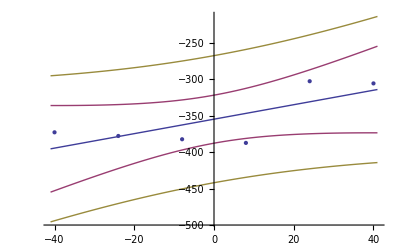

| Estimate | Standard Error | Confidence Interval
1 | -355. | 11.85 | {-387.901,-322.099}
x | 0.991071 | 0.433666 | {-0.212978,2.19512}

842.536

{795.492,1123.09,967.492,458.19,746.873,1062.09}

```mathematica
Show[{
Plot[{BestFit[1,x],BestFit["MeanPredictionBands"],BestFit["SinglePredictionBands"]},{x,Min[ListZ]-1,Max[ListZ]+1}],
ListPlot[ListY]
}]
BestFit["ParameterConfidenceIntervalTable"]
BestFit["EstimatedVariance"]
BestFit["SingleDeletionVariances"]
```

```mathematica
BestFit["BasisFunctions"]
BestFit["BestFit"]
BestFit["Data"]
BestFit["DesignMatrix"]
BestFit["Function"]
BestFit["Response"]
BestFit["BestFitParameters"]
```

{1,x}

2.51429+0.654286 x

{{{1.,0.},{1.,1.},{1.,2.},{1.,3.},{1.,4.},{1.,5.}},{1,6,3.,3.9,5,6}}

{{1.,0.},{1.,1.},{1.,2.},{1.,3.},{1.,4.},{1.,5.}}

2.51429 #1+0.654286 #2&

{1,6,3.,3.9,5,6}

{2.51429,0.654286}

```mathematica
(* Residual *)
BestFit["FitResiduals"]
```

{-1.51429,2.83143,-0.822857,-0.577143,-0.131429,0.214286}

```mathematica
BestFit["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 4288.49 | 4288.49 | 0.517366 | 0.511749
Error | 4 | 33156.3 | 8289.08 |  | 
Total | 5 | 37444.8 |  |  |

```mathematica
SSTotal=Variance[Y] (NInput-1)
SSTotal==Y.Y-NInput(Mean[Y])^2 (* total variation = (y - mean[y])^2 *)
DFTotal = NInput-1
SSR = BestFit["ANOVATableEntries"][[-2]][[2]]
SSR==BestFit["ANOVATableSumsOfSquares"][[-2]]
SSR==Norm[PMat.Y-Y]^2
SSReg = SSTotal-SSR (* variation that DOES not explained by the fit *)
MSReg=SSReg/(DFTotal-DF)
MSR=SSR/4
MSR==BestFit["ANOVATableEntries"][[-2]][[-1]]
MSR==BestFit["EstimatedVariance"]
FRatio=MSReg/MSR
1-CDF[FRatioDistribution[DFTotal-DF,DF],FRatio] (* P-Value *)
```

18.875

True

5

11.3834

True

True

7.49157

7.49157

2.84586

True

True

2.63245

0.18002

```mathematica
BestFit["CoefficientOfVariation"]
```

0.406498

```mathematica
BestFit["PartialSumOfSquares"]
BestFit["SequentialSumOfSquares"]
```

{7.49157}

{7.49157}

```mathematica
CoRel=Table[(CoVar[[i]][[j]])/(√(CoVar[[i]][[i]]CoVar[[j]][[j]])),{i,1,NPara},{j,1,NPara}];CoRel//N//MatrixForm
CoRel==BestFit["CorrelationMatrix"]
CV=CoVar MSR;CV//N//MatrixForm
CV==BestFit["CovarianceMatrix"]
```

(1. | -0.825723
-0.825723 | 1.)

True

(1.49069 | -0.406551
-0.406551 | 0.16262)

True

```mathematica
BestFit["EigenstructureTable"]
```

Eigenvalue | Index | x
1. | 1. | 1.

```mathematica
BestFit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 2.51429 | 1.22094 | 2.05931 | 0.108538
x | 0.654286 | 0.403262 | 1.62248 | 0.18002

```mathematica
β=GMat.Y
σβ={√(CoVar[[1]][[1]] MSR),√(CoVar[[2]][[2]] MSR)}
tStat=GMat.Y/{√(CoVar[[1]][[1]] MSR),√(CoVar[[2]][[2]] MSR)}
{(1-CDF[StudentTDistribution[DF],tStat[[1]]])2, (1-CDF[StudentTDistribution[DF],tStat[[2]]])2}
(* the p-value is the 2-Tails chance that the Estimate value difference from zero, with standard Error = 1, not quite useful *)
```

{2.51429,0.654286}

{1.22094,0.403262}

{2.05931,1.62248}

{0.108538,0.18002}

```mathematica
BestFit["ParameterConfidenceIntervalTable"]
α=0.95;
InverseCDF[StudentTDistribution[DF],(1+α)/2]
β[[1]]+{InverseCDF[StudentTDistribution[DF],(1-α)/2],InverseCDF[StudentTDistribution[DF],(1+α)/2]}σβ[[1]]
β[[2]]+{InverseCDF[StudentTDistribution[DF],(1-α)/2],InverseCDF[StudentTDistribution[DF],(1+α)/2]}σβ[[2]]
```

| Estimate | Standard Error | Confidence Interval
1 | -264.983 | 37.1687 | {-368.18,-161.786}
x | 0.978393 | 1.36024 | {-2.79823,4.75501}

2.77645

{-0.875579,5.90415}

{-0.46535,1.77392}

```mathematica
RSq=SSReg/(SSR+SSReg)
RSq==BestFit["RSquared"]
AdjRSq=1-(SSR/DF)/(SSTotal/DFTotal)
AdjRSq==BestFit["AdjustedRSquared"]
```

0.396904

True

0.246131

True

```mathematica
BestFit["MeanPredictionConfidenceIntervalTable"]
Yhat=PMat.Y
σYhat=Table[√(PMat[[i]][[i]] MSR),{i,1,NInput}]
Table[Yhat[[i]]+{InverseCDF[StudentTDistribution[DF],(1-α)/2],InverseCDF[StudentTDistribution[DF],(1+α)/2]}σYhat[[i]],{i,1,NInput}]
```

Observed | Predicted | Standard Error | Confidence Interval
1 | 2.51429 | 1.22094 | {-0.875579,5.90415}
6 | 3.16857 | 0.916627 | {0.623606,5.71354}
3. | 3.82286 | 0.71761 | {1.83045,5.81526}
3.9 | 4.47714 | 0.71761 | {2.48474,6.46955}
5 | 5.13143 | 0.916627 | {2.58646,7.67639}
6 | 5.78571 | 1.22094 | {2.39585,9.17558}

{2.51429,3.16857,3.82286,4.47714,5.13143,5.78571}

{1.22094,0.916627,0.71761,0.71761,0.916627,1.22094}

{{-0.875579,5.90415},{0.623606,5.71354},{1.83045,5.81526},{2.48474,6.46955},{2.58646,7.67639},{2.39585,9.17558}}

```mathematica
Norm[(BestFit["Response"]-BestFit["PredictedResponse"])/BestFit["MeanPredictionErrors"]]^2/DF
```

2.95238

```mathematica
BestFit["MeanPredictionErrors"]
```

{0.0748331,0.052915,0.0432049,0.052915,0.0748331}

```mathematica
BestFit["MeanPredictionBands"]
BestFit["SinglePredictionBands"]
```

{1.02+1. x-3.18245 √(0.0056-0.00373333 x+0.000933333 x^2),1.02+1. x+3.18245 √(0.0056-0.00373333 x+0.000933333 x^2)}

{1.02+1. x-3.18245 √(0.0149333-0.00373333 x+0.000933333 x^2),1.02+1. x+3.18245 √(0.0149333-0.00373333 x+0.000933333 x^2)}

```mathematica
(* Variance of residual *)
e=BestFit["FitResiduals"]
σe=Table[√((1-PMat[[i]][[i]]) MSR),{i,1,NInput}]
se=e/σe
se==BestFit["StandardizedResiduals"]
MSRi= Table[((DF)MSR-e[[i]]^2/(1-PMat[[i]][[i]]))/(DF-1),{i,1,NInput}]
MSRi==BestFit["SingleDeletionVariances"]
ste=Table[e[[i]]/(√((1-PMat[[i]][[i]]) MSRi[[i]])),{i,1,NInput}]
ste==BestFit["StudentizedResiduals"]
```

{-1.51429,2.83143,-0.822857,-0.577143,-0.131429,0.214286}

{1.16412,1.41621,1.52673,1.52673,1.41621,1.16412}

{-1.3008,1.9993,-0.538968,-0.378026,-0.092803,0.184076}

True

{2.18933,0.00265766,3.51891,3.65891,3.78631,3.76233}

False

{-1.48307,65.4237,-0.484692,-0.33339,-0.0804564,0.160094}

False

```mathematica
BestFit["AIC"]
BestFit["BIC"]
```

26.8697

26.2449

```mathematica
Table[MSRi[[i]]^NPara/(MSR^NPara(1-PMat[[i]][[i]])),{i,1,NInput}] (* ratio of determinet of covariance matrix *)
BestFit["CovarianceRatios"]
Table[1+3 (NPara+1)/NInput//N,{i,1,NInput}]
```

{1.24284,1.23746×10^-6,1.86673,2.01822,2.51167,3.67035}

{1.24284,1.23746×10^-6,1.86673,2.01822,2.51167,3.67035}

{2.5,2.5,2.5,2.5,2.5,2.5}

```mathematica
Table[PMat[[i]][[i]],{i,1,NInput}]//N
BestFit["HatDiagonal"]
```

{0.52381,0.295238,0.180952,0.180952,0.295238,0.52381}

{0.52381,0.295238,0.180952,0.180952,0.295238,0.52381}